```mathematica
ids={"5762298832486400","5199348879065088","5104011879383040","5634601401712640","5688687119564800","5173627930542080","5646521009700864","5672188833169408","5719707252424704","5701394610782208","5658753101725696","5736577883963392","5672878150254592","5767202099691520","5700228501995520","5666961832804352","5721191432060928","5740216795004928","5712818124881920","5654595548217344","5655358173347840","5753798823772160","5707300165648384","5711261467672576","5664284977659904","5128666635829248","5640136574369792","5691616589250560","5069252692279296","5705148370255872","5206956054675456","5769906008096768","5201331526565888","5723974822526976","4919856549855232","5114556594520064","5142198416834560","5686487861428224","5749730717990912","5632202645700608","5153306812874752","5675918433452032","5758196635402240","5199033182191616","5664810037411840","5743365039587328","5716256766296064","4860723440123904","5764281479987200","6327231433408512","5708939920408576","5643517367943168","5671536392404992","5674069752020992","5635093192245248","5738275486564352","5724822843686912","5633494390669312","5118639615246336","5070544437248000","5683257223938048","5753050442498048","5705718560718848","5704221898833920","5751646390845440","5641462360309760","5651757665353728","5684793748488192","5670377556541440","5734743547052032","5758048710688768","5722152447770624","5681589568667648","5754980359208960","5701751084679168","5471866718257152","5732910535540736","4868028676177920","5684961520648192","5075454121738240","5182111044599808","5638404075159552","5753341694967808","6220853180104704","5663684521099264","5682238511382528","5662069344960512","5094953273262080","6597766625099776","5648334039547904","5131065358286848","6226234774126592"};
```

```mathematica
urls="http://www.ultianalytics.com/rest/view/team/"<>#<>"/stats/export"&/@ids;
```

```mathematica
keys=Drop[Import[urls[[1]]][[1]],-10]
```

```mathematica
keys={"Date/Time","Tournamemnt","Opponent","Point Elapsed Seconds","Line","Our Score - End of Point","Their Score - End of Point","Event Type","Action","Passer","Receiver","Defender","Hang Time (secs)","Player 0","Player 1","Player 2","Player 3","Player 4","Player 5","Player 6","Player 7","Player 8","Player 9","Player 10","Player 11","Player 12","Player 13","Player 14","Player 15","Player 16","Player 17","Player 18","Player 19","Player 20","Player 21","Player 22","Player 23","Player 24","Player 25","Player 26","Player 27","Elapsed Time (secs)"};
```

Make the raw dataset for team number 4 with id→“5634601401712640”

```mathematica
rawwebsite=Import["C:\\Users\\praha\\Documents\\Wolfram Mathematica\\UltiAnalytics.html","XMLObject"];
```

```mathematica
idsdata17=rawwebsite[[2,3,2,3,4,3,6,3,2,3,4]];
```

```mathematica
idsdata16=rawwebsite[[2,3,2,3,4,3,6,3,2,3,6,3,2,3,4]];
```

```mathematica
idsdata15=rawwebsite[[2,3,2,3,4,3,6,3,2,3,6,3,4,3,4]];
```

```mathematica
idsdata14=rawwebsite[[2,3,2,3,4,3,6,3,2,3,6,3,6,3,4]];
```

```mathematica
StringLength["http://www.ultianalytics.com/app/#/5471866718257152"]
```

```mathematica
51
(* Need to match the id with the team name *)
```

```mathematica
ids=StringTake[#,36;;51]&/@Cases[{idsdata14,idsdata15,idsdata16,idsdata17},HoldPattern["href"->_],Infinity][[All,2]]
```

{5471866718257152,5732910535540736,4868028676177920,5684961520648192,5075454121738240,5182111044599808,5638404075159552,5753341694967808,6220853180104704,5663684521099264,5682238511382528,5662069344960512,5094953273262080,6597766625099776,5648334039547904,5131065358286848,6226234774126592,5708939920408576,5643517367943168,5671536392404992,5674069752020992,5635093192245248,5738275486564352,5724822843686912,5633494390669312,5118639615246336,5070544437248000,5683257223938048,5753050442498048,5705718560718848,5704221898833920,5751646390845440,5641462360309760,5651757665353728,5684793748488192,5670377556541440,5734743547052032,5758048710688768,5722152447770624,5681589568667648,5754980359208960,5701751084679168,5664284977659904,5128666635829248,5640136574369792,5691616589250560,5069252692279296,5705148370255872,5206956054675456,5769906008096768,5201331526565888,5723974822526976,4919856549855232,5114556594520064,5142198416834560,5686487861428224,5749730717990912,5632202645700608,5153306812874752,5675918433452032,5758196635402240,5199033182191616,5664810037411840,5743365039587328,5716256766296064,4860723440123904,5764281479987200,6327231433408512,5762298832486400,5199348879065088,5104011879383040,5634601401712640,5688687119564800,5173627930542080,5646521009700864,5672188833169408,5719707252424704,5701394610782208,5658753101725696,5736577883963392,5672878150254592,5767202099691520,5700228501995520,5666961832804352,5721191432060928,5740216795004928,5712818124881920,5654595548217344,5655358173347840,5753798823772160,5707300165648384,5711261467672576}

```mathematica
names=Flatten@Cases[{idsdata14,idsdata15,idsdata16,idsdata17},{_String},Infinity]
```

{Chicago Wildfire,Cincinnati Revolution,DC Breeze,Detroit Mechanix,Indianapolis AlleyCats,Madison Radicals,Minnesota Wind Chill,Montreal Royal,New York Empire,Philadelphia Phoenix,Rochester Dragons,Salt Lake Lions,San Francisco FlameThrowers,San Jose Spiders,Seattle Raptors,Toronto Rush,Vancouver Riptide,Atlanta Hustle,Charlotte Express,Chicago Wildfire,Cincinnati Revolution,DC Breeze,Detroit Mechanix,Indianapolis AlleyCats,Jacksonville Cannons,Los Angeles Aviators,Madison Radicals ,Minnesota Wind Chill ,Montreal Royal,Nashville Nightwatch,New York Empire,Ottawa Outlaws ,Philadelphia Phoenix,Pittsburgh Thunderbirds,Raleigh Flyers ,Rochester Dragons,San Diego Growlers,San Francisco FlameThrowers,San Jose Spiders,Seattle Cascades,Toronto Rush ,Vancouver Riptide,Atlanta Hustle,Austin Sol,Charlotte Express,Chicago Wildfire,Cincinnati Revolution,DC Breeze,Dallas Roughnecks,Detroit Mechanix,Indianapolis AlleyCats,Jacksonville Cannons,Los Angeles Aviators,Madison Radicals ,Minnesota Wind Chill ,Montreal Royal,Nashville Nightwatch,New York Empire,Ottawa Outlaws ,Philadelphia Phoenix,Pittsburgh Thunderbirds,Raleigh Flyers ,San Diego Growlers,San Francisco FlameThrowers,San Jose Spiders,Seattle Cascades,Toronto Rush ,Vancouver Riptide,Atlanta Hustle,Austin Sol,Chicago Wildfire,DC Breeze,Dallas Roughnecks,Detroit Mechanix,Indianapolis AlleyCats,Jacksonville Cannons,Los Angeles Aviators,Madison Radicals ,Minnesota Wind Chill ,Montreal Royal,Nashville Nightwatch,New York Empire,Ottawa Outlaws ,Philadelphia Phoenix,Pittsburgh Thunderbirds,Raleigh Flyers ,San Diego Growlers,San Francisco FlameThrowers,San Jose Spiders,Seattle Cascades,Toronto Rush ,Vancouver Riptide}

```mathematica
Cases[Cases[rawwebsite,HoldPattern["href"->_],Infinity][[All,2]],"http://www.ultianalytics.com/app/#/"~~___~~"/players"]
```

{}

```mathematica
Cases[rawwebsite,HoldPattern["href"->"http://www.ultianalytics.com/app/#/"<>_<>"/players"],Infinity]
```

{}

```mathematica
rawdataset4=Dataset[Association[Thread[keys->#]]&/@Drop[Import[urls[[4]]],1]]
```

Dataset[<>]

Convert Date/Time strings to WL DateObjects, and Elapsed Time in “Seconds”

```mathematica
dataset4=rawdataset4[All,{1->DateObject}][All,{-1->(Quantity[#,"Seconds"]&)}]
```

Dataset[<>]

```mathematica
path=NotebookDirectory[];
Export[path<>"dasaet4.wl",dataset4]
```

C:\Users\praha\Documents\WSS\dasaet4.wl

```mathematica
dataset4=Import[path<>"dasaet4.wl"]
```

Dataset[<>]

```mathematica
ts4=TimeSeries[Normal[dataset4[All,6]],{QuantityMagnitude[Normal[dataset4[All,-1]]]}]
```

TimeSeries[…]

```mathematica
ts4o=TimeSeries[Normal[dataset4[All,7]],{QuantityMagnitude[Normal[dataset4[All,-1]]]}]
```

TimeSeries[…]

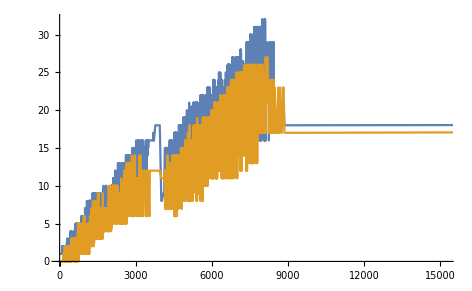

```mathematica
ListLinePlot[{ts4,ts4o}]
```

```mathematica
dataset4[1]//Normal
```

<|Date/Time→Minute: Sat 22 Apr 2017 19:00GMT-4.,Tournamemnt→AUDL 2017,Opponent→Raleigh Flyers,Point Elapsed Seconds→75,Line→O,Our Score - End of Point→1,Their Score - End of Point→0,Event Type→Offense,Action→Catch,Passer→Jon N,Receiver→Lloyd B,Defender→,Hang Time (secs)→,Player 0→Alan K,Player 1→Lloyd B,Player 2→Justin S,Player 3→Max C,Player 4→Matt K,Player 5→Jon N,Player 6→Eric M,Player 7→,Player 8→,Player 9→,Player 10→,Player 11→,Player 12→,Player 13→,Player 14→,Player 15→,Player 16→,Player 17→,Player 18→,Player 19→,Player 20→,Player 21→,Player 22→,Player 23→,Player 24→,Player 25→,Player 26→,Player 27→,Elapsed Time (secs)→0 s|>

```mathematica
dataset4[Select[#Opponent=="Raleigh Flyers"&],{6,-1}]
```

Dataset[<>]

```mathematica
ts4Ral= TimeSeries[QuantityMagnitude@Normal@Values@dataset4[Select[#Opponent=="Raleigh Flyers"&],{-1,6}]]
```

TimeSeries[…]

```mathematica
ts4RalO= TimeSeries[QuantityMagnitude@Normal@Values@dataset4[Select[#Opponent=="Raleigh Flyers"&],{-1,7}]]
```

TimeSeries[…]

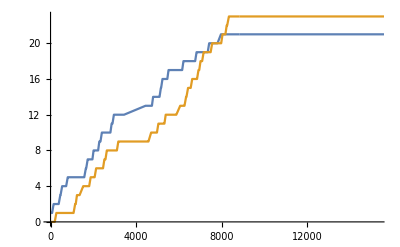

```mathematica
ListLinePlot[{ts4Ral,ts4RalO}]
```

```mathematica
TimelinePlot[DateObject[dataset4[All,1]]
```

$Aborted